```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ω/ν)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]+A*kx/ω*Exp[k*z]+B*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]+A*ky/ω*Exp[k*z]+B*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]-I*A*k/ω*Exp[k*z]+I*B*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=g*z-(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ω)/ν)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν))+(B ⅇ^(-√(kx^2+ky^2) z) kx)/ω+(A ⅇ^(√(kx^2+ky^2) z) kx)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν))+(B ⅇ^(-√(kx^2+ky^2) z) ky)/ω+(A ⅇ^(√(kx^2+ky^2) z) ky)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν))+(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/ω-(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/ω)

-ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))+g z

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-ν*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]]
Expand[D[uy[x,y,z,t],t]-ν*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]]
Expand[D[uz[x,y,z,t],t]-ν*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]-g]
```

0

0

0

```mathematica
Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]
Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]
Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z k)]
Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z k)]
```

ⅈ Ax kx+ⅈ Ay ky+Az √(kx^2+ky^2+(ⅈ ω)/ν)

ⅈ Bx kx+ⅈ By ky-Bz √(kx^2+ky^2+(ⅈ ω)/ν)

0

0

```mathematica
sol1=Solve[{ⅈ Ax kx+ⅈ Ay ky+Az √(kx^2+ky^2+(ⅈ ω)/ν)==0,ⅈ Bx kx+ⅈ By ky-Bz √(kx^2+ky^2+(ⅈ ω)/ν)==0},{Az,Bz}][[1]]
```

{Az→(ⅈ (-Ax kx-Ay ky))/(√((kx^2 ν+ky^2 ν+ⅈ ω)/ν)),Bz→(ⅈ (Bx kx+By ky))/(√((kx^2 ν+ky^2 ν+ⅈ ω)/ν))}

```mathematica
Simplify[(-g*(h[x,y,z,t]-h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.sol1]
Simplify[(I*kx*uz[x,y,z,t]-(D[ux[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.sol1]
Simplify[(I*ky*uz[x,y,z,t]-(D[uy[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.sol1]
Simplify[(I*ω*(h[x,y,z,t]-h0)+ux[x,y,z,t]*I*kx*(h[x,y,z,t]-h0)+uy[x,y,z,t]*I*ky*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.sol1]
```

1/ω ⅈ ⅇ^(-h0 (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (2 B ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) μ+2 A ⅇ^(h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ+ⅇ^(h0 √(kx^2+ky^2)) (2 ⅇ^(2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Ax kx+Ay ky) μ+2 (Bx kx+By ky) μ+ⅈ ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) H (g+(kx^2+ky^2) σ)) ω)

(B ⅇ^(-h0 √(kx^2+ky^2)) kx √(kx^2+ky^2))/ω-(A ⅇ^(h0 √(kx^2+ky^2)) kx √(kx^2+ky^2))/ω-(B ⅇ^(-√(kx^2+ky^2) z) kx √(kx^2+ky^2))/ω+(A ⅇ^(√(kx^2+ky^2) z) kx √(kx^2+ky^2))/ω+(ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)) kx (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν)) kx (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))+Bx ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-Ax ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)

(B ⅇ^(-h0 √(kx^2+ky^2)) ky √(kx^2+ky^2))/ω-(A ⅇ^(h0 √(kx^2+ky^2)) ky √(kx^2+ky^2))/ω-(B ⅇ^(-√(kx^2+ky^2) z) ky √(kx^2+ky^2))/ω+(A ⅇ^(√(kx^2+ky^2) z) ky √(kx^2+ky^2))/ω+(ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)) ky (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν)) ky (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))+By ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-Ay ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)

-(ⅈ B ⅇ^(-h0 √(kx^2+ky^2)) √(kx^2+ky^2))/ω+(ⅈ A ⅇ^(h0 √(kx^2+ky^2)) √(kx^2+ky^2))/ω+ⅈ H ω+(ⅈ ⅇ^(ⅈ (kx x+ky y+t ω)) H kx (B ⅇ^(-h0 √(kx^2+ky^2)) kx+A ⅇ^(h0 √(kx^2+ky^2)) kx+Bx ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω+Ax ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω))/ω+(ⅈ ⅇ^(ⅈ (kx x+ky y+t ω)) H ky (B ⅇ^(-h0 √(kx^2+ky^2)) ky+A ⅇ^(h0 √(kx^2+ky^2)) ky+By ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω+Ay ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω))/ω+(ⅈ ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅈ ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))

```mathematica
Simplify[Solve[{(2 B ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) μ+2 A ⅇ^(h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ+ⅇ^(h0 √(kx^2+ky^2)) (2 ⅇ^(2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Ax kx+Ay ky) μ+2 (Bx kx+By ky) μ+ⅈ ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) H (g+(kx^2+ky^2) σ)) ω)==0,(B ⅇ^(-h0 √(kx^2+ky^2)) kx √(kx^2+ky^2))/ω-(A ⅇ^(h0 √(kx^2+ky^2)) kx √(kx^2+ky^2))/ω-(B ⅇ^(-√(kx^2+ky^2) z) kx √(kx^2+ky^2))/ω+(A ⅇ^(√(kx^2+ky^2) z) kx √(kx^2+ky^2))/ω+(ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)) kx (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν)) kx (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))+Bx ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-Ax ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)==0,(B ⅇ^(-h0 √(kx^2+ky^2)) ky √(kx^2+ky^2))/ω-(A ⅇ^(h0 √(kx^2+ky^2)) ky √(kx^2+ky^2))/ω-(B ⅇ^(-√(kx^2+ky^2) z) ky √(kx^2+ky^2))/ω+(A ⅇ^(√(kx^2+ky^2) z) ky √(kx^2+ky^2))/ω+(ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)) ky (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅇ^(-z √(kx^2+ky^2+(ⅈ ω)/ν)) ky (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))+By ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-Ay ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)==0,-(ⅈ B ⅇ^(-h0 √(kx^2+ky^2)) √(kx^2+ky^2))/ω+(ⅈ A ⅇ^(h0 √(kx^2+ky^2)) √(kx^2+ky^2))/ω+ⅈ H ω+(ⅈ ⅇ^(ⅈ (kx x+ky y+t ω)) H kx (B ⅇ^(-h0 √(kx^2+ky^2)) kx+A ⅇ^(h0 √(kx^2+ky^2)) kx+Bx ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω+Ax ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω))/ω+(ⅈ ⅇ^(ⅈ (kx x+ky y+t ω)) H ky (B ⅇ^(-h0 √(kx^2+ky^2)) ky+A ⅇ^(h0 √(kx^2+ky^2)) ky+By ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω+Ay ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω))/ω+(ⅈ ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Ax kx+Ay ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))-(ⅈ ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (Bx kx+By ky))/(√(kx^2+ky^2+(ⅈ ω)/ν))==0},{A,Ay,B,By}]]
```

{{A→(ⅇ^(h0 √(kx^2+ky^2)) ω (2 ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+ⅈ t ω+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) H^2 kx √(kx^2+ky^2) (g+(kx^2+ky^2) σ) (kx^2 ν+ky^2 ν+ⅈ ω)+4 ⅇ^(2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) H kx √(kx^2+ky^2) μ (kx^2 ν+ky^2 ν+ⅈ ω) ω-4 ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) H kx √(kx^2+ky^2) μ (kx^2 ν+ky^2 ν+ⅈ ω) ω+2 ⅇ^(ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) H^2 kx √(kx^2+ky^2) (g+(kx^2+ky^2) σ) (-ⅈ kx^2 ν-ⅈ ky^2 ν+ω)+4 Bx ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν)-4 Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν)-ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) H^2 kx (kx^2+ky^2) ν (g+(kx^2+ky^2) σ) √(kx^2+ky^2+(ⅈ ω)/ν)+ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω+h0 √(kx^2+ky^2+(ⅈ ω)/ν)+2 z √(kx^2+ky^2+(ⅈ ω)/ν)) H^2 kx (kx^2+ky^2) ν (g+(kx^2+ky^2) σ) √(kx^2+ky^2+(ⅈ ω)/ν)+4 ⅈ Bx ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) μ ω √(kx^2+ky^2+(ⅈ ω)/ν)-4 ⅈ Ax ⅇ^(3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) μ ω √(kx^2+ky^2+(ⅈ ω)/ν)-ⅈ ⅇ^(h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (g √(kx^2+ky^2)+(kx^2+ky^2) (√(kx^2+ky^2) σ-2 ⅈ μ ω))+ⅇ^(√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (ⅈ g √(kx^2+ky^2)+(kx^2+ky^2) (ⅈ √(kx^2+ky^2) σ+2 μ ω))-2 Bx ⅇ^(z (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ ν (-kx^2-ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))+2 Ax ⅇ^(2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ ν (-kx^2-ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))-2 Bx ⅇ^(√(kx^2+ky^2) z+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) μ ν (kx^2+ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))+2 Ax ⅇ^(√(kx^2+ky^2) z+4 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) μ ν (kx^2+ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))))/(2 kx (kx^2+ky^2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν) (-2 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2)+2 ⅇ^(√(kx^2+ky^2) z+2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2)+2 ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-2 ⅇ^(2 √(kx^2+ky^2) z+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2+(ⅈ ω)/ν))),Ay→(ⅇ^(-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (ⅈ ⅇ^(3 h0 √(kx^2+ky^2)+ⅈ kx x+ⅈ ky y+ⅈ t ω+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) H √(kx^2+ky^2) (g+(kx^2+ky^2) σ)-2 ⅈ ⅇ^(2 h0 √(kx^2+ky^2)+ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) H √(kx^2+ky^2) (g+(kx^2+ky^2) σ)+ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+2 √(kx^2+ky^2) z+ⅈ t ω+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) H √(kx^2+ky^2) (g+(kx^2+ky^2) σ)+4 ⅇ^((2 h0+z) (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) μ ω-ⅈ ⅇ^(z (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) (g+kx^2 σ+ky^2 σ-2 ⅈ √(kx^2+ky^2) μ ω)+ⅈ ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) (g+kx^2 σ+ky^2 σ+2 ⅈ √(kx^2+ky^2) μ ω))+2 Bx ⅇ^(h0 (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) μ (-2 ⅇ^(√(kx^2+ky^2) z+h0 (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) ν+2 ⅈ ⅇ^(h0 √(kx^2+ky^2)+z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) ω+ⅇ^(z (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) ν (√(kx^2+ky^2)-√(kx^2+ky^2+(ⅈ ω)/ν))+ⅇ^(2 h0 √(kx^2+ky^2)+z √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) ν (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν)))+Ax (4 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+2 z √(kx^2+ky^2+(ⅈ ω)/ν)) kx^2 √(kx^2+ky^2) μ ν+4 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+4 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ky^2 √(kx^2+ky^2) μ ν-4 ⅈ ⅇ^(z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (2 √(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) μ ω+ⅇ^(3 h0 √(kx^2+ky^2)+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) (-2 ky^2 μ ν (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+kx^2 μ ν (-2 √(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν)))+ⅇ^(z (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) (-2 kx^2 μ ν (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+ky^2 μ ν (-2 √(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))))))/(2 kx ky μ ν (2 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2)-2 ⅇ^(√(kx^2+ky^2) z+2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2)-2 ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)+2 ⅇ^(2 √(kx^2+ky^2) z+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2+(ⅈ ω)/ν))),B→(ⅇ^(√(kx^2+ky^2) (h0+z)-h0 √(kx^2+ky^2+(ⅈ ω)/ν)) ω (2 ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) H^2 kx √(kx^2+ky^2) (g+(kx^2+ky^2) σ) (kx^2 ν+ky^2 ν+ⅈ ω)+4 ⅇ^(2 h0 √(kx^2+ky^2)+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) H kx √(kx^2+ky^2) μ (kx^2 ν+ky^2 ν+ⅈ ω) ω-4 ⅇ^(z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) H kx √(kx^2+ky^2) μ (kx^2 ν+ky^2 ν+ⅈ ω) ω+2 ⅇ^(2 h0 √(kx^2+ky^2)+ⅈ kx x+ⅈ ky y+ⅈ t ω+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) H^2 kx √(kx^2+ky^2) (g+(kx^2+ky^2) σ) (-ⅈ kx^2 ν-ⅈ ky^2 ν+ω)+4 Bx ⅇ^(z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν)-4 Ax ⅇ^(z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))+h0 (√(kx^2+ky^2)+4 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν)-ⅈ ⅇ^(2 h0 √(kx^2+ky^2)+ⅈ kx x+ⅈ ky y+ⅈ t ω+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+2 z √(kx^2+ky^2+(ⅈ ω)/ν)) H^2 kx (kx^2+ky^2) ν (g+(kx^2+ky^2) σ) √(kx^2+ky^2+(ⅈ ω)/ν)+ⅈ ⅇ^(ⅈ (kx x+ky y+t ω)+h0 (2 √(kx^2+ky^2)+4 √(kx^2+ky^2+(ⅈ ω)/ν))) H^2 kx (kx^2+ky^2) ν (g+(kx^2+ky^2) σ) √(kx^2+ky^2+(ⅈ ω)/ν)+4 ⅈ Bx ⅇ^(2 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2) μ ω √(kx^2+ky^2+(ⅈ ω)/ν)-4 ⅈ Ax ⅇ^(2 h0 √(kx^2+ky^2)+4 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2) μ ω √(kx^2+ky^2+(ⅈ ω)/ν)+ⅈ ⅇ^(h0 (2 √(kx^2+ky^2)+4 √(kx^2+ky^2+(ⅈ ω)/ν))) H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (g √(kx^2+ky^2)+(kx^2+ky^2) (√(kx^2+ky^2) σ+2 ⅈ μ ω))+ⅇ^(2 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+2 z √(kx^2+ky^2+(ⅈ ω)/ν)) H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (-ⅈ g √(kx^2+ky^2)+(kx^2+ky^2) (-ⅈ √(kx^2+ky^2) σ+2 μ ω))-2 Bx ⅇ^(h0 (2 √(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ ν (-kx^2-ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))+2 Ax ⅇ^(h0 (2 √(kx^2+ky^2)+5 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ ν (-kx^2-ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))+2 Ax ⅇ^(2 h0 √(kx^2+ky^2)+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+2 z √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) μ ν (kx^2+ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))-2 Bx ⅇ^(2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) μ ν (kx^2+ky^2+√(kx^2+ky^2) √(kx^2+ky^2+(ⅈ ω)/ν))))/(2 kx (kx^2+ky^2) μ ν √(kx^2+ky^2+(ⅈ ω)/ν) (-2 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2)+2 ⅇ^(√(kx^2+ky^2) z+2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2)+2 ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)-2 ⅇ^(2 √(kx^2+ky^2) z+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2+(ⅈ ω)/ν))),By→(ⅇ^(z √(kx^2+ky^2+(ⅈ ω)/ν)) (ⅇ^(h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) (ⅇ^(h0 √(kx^2+ky^2))-ⅇ^(√(kx^2+ky^2) z)) H kx ν √(kx^2+ky^2+(ⅈ ω)/ν) (-ⅈ ⅇ^(ⅈ kx x+ⅈ ky y+√(kx^2+ky^2) z+ⅈ t ω) H √(kx^2+ky^2) (g+(kx^2+ky^2) σ)+ⅈ ⅇ^(h0 √(kx^2+ky^2)+ⅈ (kx x+ky y+t ω)) H √(kx^2+ky^2) (g+(kx^2+ky^2) σ)+ⅈ ⅇ^(h0 √(kx^2+ky^2)) (g+kx^2 σ+ky^2 σ+2 ⅈ √(kx^2+ky^2) μ ω)+ⅇ^(√(kx^2+ky^2) z) (ⅈ g+ⅈ kx^2 σ+ⅈ ky^2 σ+2 √(kx^2+ky^2) μ ω))-2 Ax ⅇ^(h0 (√(kx^2+ky^2)+3 √(kx^2+ky^2+(ⅈ ω)/ν))) μ (-2 ⅇ^(h0 √(kx^2+ky^2)+z (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2)^(3/2) ν+2 ⅈ ⅇ^(√(kx^2+ky^2) z+h0 (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) ω+ⅇ^(h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2+ky^2) ν (√(kx^2+ky^2)-√(kx^2+ky^2+(ⅈ ω)/ν))+ⅇ^(2 √(kx^2+ky^2) z+h0 √(kx^2+ky^2+(ⅈ ω)/ν)) (kx^2+ky^2) ν (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))))+Bx (-4 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) kx^2 √(kx^2+ky^2) μ ν-4 ⅇ^(√(kx^2+ky^2) z+2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) ky^2 √(kx^2+ky^2) μ ν+4 ⅈ ⅇ^((2 h0+z) (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2) μ ω+ⅇ^(2 √(kx^2+ky^2) z+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) (kx^2 μ ν (2 √(kx^2+ky^2)-2 √(kx^2+ky^2+(ⅈ ω)/ν))+2 ky^2 μ ν (√(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν)))+ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) (2 ky^2 μ ν (√(kx^2+ky^2)-√(kx^2+ky^2+(ⅈ ω)/ν))+kx^2 μ ν (2 √(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν)))))/(2 kx ky μ ν (2 ⅇ^(2 h0 √(kx^2+ky^2)+√(kx^2+ky^2) z+3 h0 √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2)-2 ⅇ^(√(kx^2+ky^2) z+2 z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (2 √(kx^2+ky^2)+√(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2)-2 ⅇ^(3 h0 √(kx^2+ky^2)+2 h0 √(kx^2+ky^2+(ⅈ ω)/ν)+z √(kx^2+ky^2+(ⅈ ω)/ν)) √(kx^2+ky^2+(ⅈ ω)/ν)+2 ⅇ^(2 √(kx^2+ky^2) z+z √(kx^2+ky^2+(ⅈ ω)/ν)+h0 (√(kx^2+ky^2)+2 √(kx^2+ky^2+(ⅈ ω)/ν))) √(kx^2+ky^2+(ⅈ ω)/ν)))}}

### Thin film

```mathematica
Clear[σ]
Clear[ρ]
Clear[μ]
H[x_,t_]:=H0+h*Exp[I*k*x+I*s*t]
Hs[x_]:=As*Sin[ks*x];
```

```mathematica
mat=FullSimplify[Table[Expand[TrigToExp[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]]]/.Exp[u_]:>Exp[Expand[u]]/.Exp[a_]:>0,{n,-3,3},{m,-1,1}]/.h->1]
```

{{-(ad As^3 k (k-3 ks) ρ)/(48 μ),(ⅈ As^3 k (k-3 ks) (g ρ+k^2 σ))/(24 μ),(ad As^3 k (k-3 ks) ρ)/(48 μ)},{-(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ),-(As^2 H0 k (k-2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ)},{(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ),-(ⅈ As (As^2+4 H0^2) k (k-ks) (g ρ+k^2 σ))/(8 μ),-(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ)},{(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ),ⅈ s+(H0 (3 As^2+2 H0^2) k^2 (g ρ+k^2 σ))/(6 μ),-(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ)},{-(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ),(ⅈ As (As^2+4 H0^2) k (k+ks) (g ρ+k^2 σ))/(8 μ),(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ)},{-(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ),-(As^2 H0 k (k+2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ)},{(ad As^3 k (k+3 ks) ρ)/(48 μ),-(ⅈ As^3 k (k+3 ks) (g ρ+k^2 σ))/(24 μ),-(ad As^3 k (k+3 ks) ρ)/(48 μ)}}

```mathematica
n=-2;
m=1;
AbsoluteTiming[Simplify[h*mat[[n+4,m+2]]/(Integrate[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]*Evaluate[Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]],{x,0,2*Pi/ks},{t,0,2*Pi/ωd}]/(2*Pi/ks)/(2*Pi/ωd))]]
```

{59.808,1}

```mathematica
μ=10^-3;
ρ=1;
σ=72;
g=980;
H0=0.1;
As=0.8*H0;
M2=5;
A[k_,ks_,ad_]=-ArrayFlatten[-I*Table[If[Abs[n1-n2]<=3&&Abs[m1-m2]<=1,(mat[[n1-n2+4,m1-m2+2]]/.k->k-n1*ks),0],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]/.s->0];
```

```mathematica
Dimensions[A[k,ks,ad]]
```

{121,121}

```mathematica
A[k,ks,ad]
```

{{(0.+0.653333 ⅈ) (980+72 (k-5 ks)^2) (k-5 ks)^2,(-0.326667+0. ⅈ) ad (k-5 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (980+72 (k-4 ks)^2) (k-5 ks) (k-4 ks),(0.+0.232 ⅈ) ad (k-5 ks) (k-4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (980+72 (k-3 ks)^2) (k-5 ks) (k-3 ks),(0.08+0. ⅈ) ad (k-5 ks) (k-3 ks),0,0,0,0,0,0,0,0,0,55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},119,{0,119,1}}
 |  |  |  |

```mathematica
A[k,ks,ad][[12]]
```

{(-0.464+0. ⅈ) (k+4 ks) (k+5 ks) (980+72 (k+4 ks)^2),(0.-0.232 ⅈ) ad (k+4 ks) (k+5 ks),0,0,0,0,0,0,0,0,0,(0.+0.653333 ⅈ) (k+4 ks)^2 (980+72 (k+4 ks)^2),(-0.326667+0. ⅈ) ad (k+4 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (k+3 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.+0.232 ⅈ) ad (k+3 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (k+2 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.08+0. ⅈ) ad (k+2 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(-0.0213333+0. ⅈ) (k+ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.-0.0106667 ⅈ) ad (k+ks) (k+4 ks),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

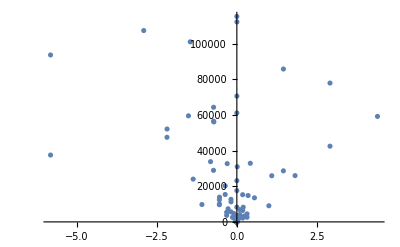

```mathematica
ListPlot[{Re[#],Im[#]}&/@Eigenvalues[A[0.5,1.0, 1000]],PlotRange->All]
```

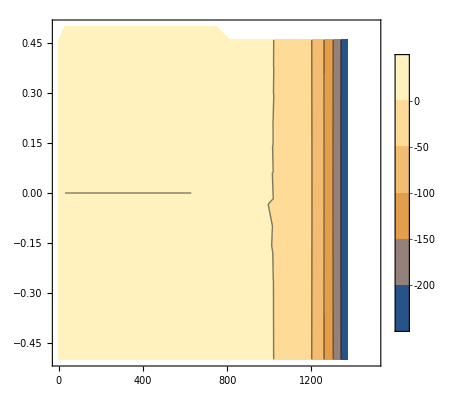

```mathematica
num=50;
Monitor[
vals=Table[{ad,k,MinimalBy[{Re[#],Im[#]}&/@Eigenvalues[A[k,1.0,ad]],#[[2]]&][[1,2]]},{ad,0,1500,1500/num},{k,-1/2,1/2,1.0/num}];,{ad,k}]
ListContourPlot[Flatten[vals,1],PlotLegends->True]
```

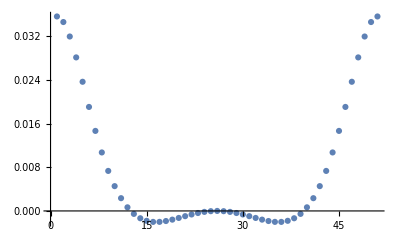

```mathematica
ListPlot[vals[[num/2+10,All,3]]]
```

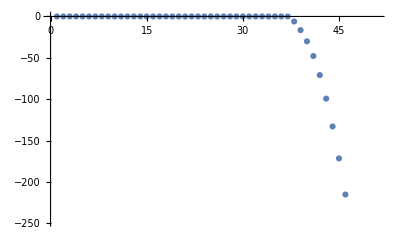

```mathematica
ListPlot[vals[[All,num/2+1,3]]]
```